```mathematica
faxc[n_,t_]:=Sum[(n/j)^(1/2)(t (E^(t Log[n/j] I)+E^(-t Log[n/j] I) )-(1/(2I))((n/j)^(t I)-(n/j)^(-t I))),{j,1,n}]
```

```mathematica
fa[n_,t_]:=Sum[j^(-1/2)(2t Cos[t Log[n/j]]-Sin[t Log[n/j]]),{j,1,n}]
fa2[n_,t_]:=fa[n,t]/((-t I+1/2)n^(t I  )+(-t I -1/2)n^(-t I))/I
fa3[n_,t_]:=fa[n,t]/(2t Cos[t Log[n]]-Sin[t Log[n]])
fa4[n_,s_]:=Sum[j^(-1/2) ((s+1/2)(n/j)^-s+(s-1/2)(n/j)^s)/((s+1/2)n^-s+(s-1/2)n^s),{j,1,n}]
fa4a[n_,s_]:=Sum[j^(-1/2) ((s I+1/2)(n/j)^-(s I)+(s I-1/2)(n/j)^(s I))/((s I+1/2)n^-(s I)+(s I-1/2)n^(s I)),{j,1,n}]
fa4b[n_,s_]:=-I Sum[j^(-1/2) ((s I+1/2)(n/j)^-(s I)+(s I-1/2)(n/j)^(s I)),{j,1,n}]
fa2a[n_,t_]:=fa[n,t]/(((t I+1/2)n^-(t I)+(t I-1/2)n^( t I)) /I)
fa2b[n_,t_]:=-fa[n,t]/( n^(-ⅈ t) (1/2 ⅈ- t))
fax[n_,t_]:=Sum[(n/j)^(1/2)(2t Cos[t Log[n/j]]-Sin[t Log[n/j]]),{j,1,n}]
fax1[n_,t_]:=Sum[(n/j)^(1/2)(2t Cos[t Log[n/j]]),{j,1,n}]
fax2[n_,t_]:=Sum[(n/j)^(1/2)(Sin[t Log[n/j]]),{j,1,n}]
fa2c[n_,t_]:=-fax[n,t]/( n^(1/2-ⅈ t) (1/2 ⅈ- t))
fa2ca[n_,t_]:=-1/( n^(1/2-ⅈ t) (1/2 ⅈ- t))
```

```mathematica
fa2[100000,30+.2I]
```

0.136341+0.538241 ⅈ

```mathematica
Zeta[.7+30I]
```

0.145667-0.547036 ⅈ

```mathematica
fa4[100000,.2+30I]
```

0.136341-0.538241 ⅈ

```mathematica
fa4a[100000,.2 I-30]
```

0.136341-0.538241 ⅈ

```mathematica
fa2a[100000,30+.2I]
```

0.136341+0.538241 ⅈ

```mathematica
fa3[100000,.2 I-30]
```

0.136341-0.538241 ⅈ

```mathematica
fa2b[100000,30+.2I]
```

0.139429+0.542857 ⅈ

```mathematica
FullSimplify[(((t I+1/2)n^-(t I)) I)]
```

1/2 n^(-ⅈ t) (ⅈ-2 t)

```mathematica
fa2c[100000,30+.2I]
```

0.139429+0.542857 ⅈ

```mathematica
fa2c[100000,N@Im@ZetaZero@1]
```

0.00261645-0.00177248 ⅈ

```mathematica
fax[100000,N@Im@ZetaZero@1]
```

14.1347

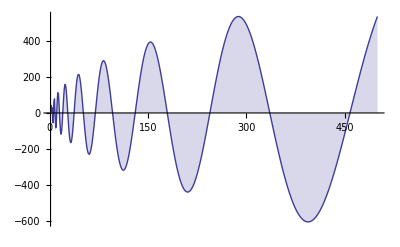

```mathematica
DiscretePlot[Re@fax[n,10],{n,1,500}]
```

```mathematica
Zeta[.5+10I]
```

1.5449-0.115336 ⅈ

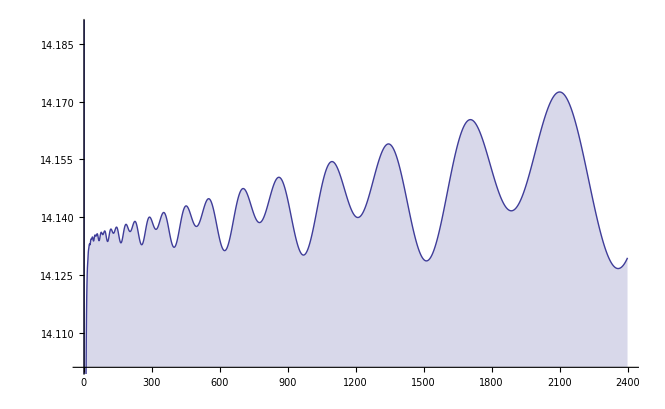

```mathematica
DiscretePlot[Abs@fax[n,N@Im@ZetaZero@1+.001I],{n,1,2400}]
```

```mathematica
N@Im@ZetaZero@1
```

14.1347

```mathematica
DiscretePlot[Re@fax1[n,N@Im@ZetaZero@10000],{n,1,2400}]
```

```mathematica
DiscretePlot[Re@fax2[n,N@Im@ZetaZero@10000],{n,1,2400}]
```

```mathematica
fax2[240000,N@Im@ZetaZero@1+.001I]
```

16958.2-0.890911 ⅈ

```mathematica
fax1[240000,N@Im@ZetaZero@1+.001I]
```

16972.5+5.58088 ⅈ

```mathematica
fax[240000,N@Im@ZetaZero@1+.001I]
```

14.2402+6.47179 ⅈ

```mathematica
faxa[n_,t_]:=Sum[(n/j)^(1/2)(2t Cos[t Log[n/j]]-Sin[t Log[n/j]]),{j,1,n}]
faxb[n_,t_]:=Sum[(n/j)^(1/2)(t (E^(t Log[n/j] I)+E^(-t Log[n/j] I) )-(1/(2I))(E^(t Log[n/j]I)-E^(-t Log[n/j]I))),{j,1,n}]
faxc[n_,t_]:=Sum[(n/j)^(1/2)(t (E^(t Log[n/j] I)+E^(-t Log[n/j] I) )-(1/(2I))((n/j)^(t I)-(n/j)^(-t I))),{j,1,n}]
faxd[n_,t_]:=Sum[(n/j)^(1/2)(t ((n/j)^(t I)+(n/j)^(-t I) )-(1/(2I))((n/j)^(t I)-(n/j)^(-t I))),{j,1,n}]
faxe[n_,t_,a_]:=Sum[(n/j)^(1/2)((t+a I) ((n/j)^((t+a I) I)+(n/j)^(-(t+a I) I) )-(1/(2I))((n/j)^((t+a I) I)-(n/j)^(-(t+a I) I))),{j,1,n}]
faxf[n_,t_,a_]:=Sum[(n/j)^(1/2)((t+a I) ((n/j)^(t I - a)+(n/j)^(-t I + a) )-(1/(2I))((n/j)^(t I - a)-(n/j)^(-t I + a))),{j,1,n}]
faxg[n_,t_,a_]:=Sum[-1/2 ⅈ (n/j)^(1/2+a-ⅈ t)+ⅈ a (n/j)^(1/2+a-ⅈ t)+(n/j)^(1/2+a-ⅈ t) t+1/2 ⅈ (n/j)^(1/2-a+ⅈ t)+ⅈ a (n/j)^(1/2-a+ⅈ t)+(n/j)^(1/2-a+ⅈ t) t,{j,1,n}]
faxh[n_,t_,a_]:=Sum[1/2 (n/j)^(1/2+a-ⅈ t) (-ⅈ+2 ⅈ a+2 t)+1/2 (n/j)^(1/2-a+ⅈ t) (ⅈ+2 ⅈ a+2 t),{j,1,n}]
faxi[n_,t_,a_]:=Sum[1/2 (n/j)^(1/2)( (n/j)^(a-ⅈ t) (-ⅈ+2 ⅈ a+2 t)+(n/j)^(-a+ⅈ t) (ⅈ+2 ⅈ a+2 t)),{j,1,n}]
faxj[n_,s_]:=(-1/2-s)n^(1/2-s)HarmonicNumber[n,1/2-s]-(-1/2+s)n^(1/2+s)HarmonicNumber[n,1/2+s]
faxk[n_,A_,f_]:=(-1/2-A-ⅈ f) n^(1/2-A-ⅈ f) HarmonicNumber[n,1/2-A-ⅈ f]-(-1/2+A+ⅈ f) n^(1/2+A+ⅈ f) HarmonicNumber[n,1/2+A+ⅈ f]
faxl[n_,A_,f_]:=Sum[(-1/2-A-ⅈ f) (n/j)^(1/2-A-ⅈ f) -(-1/2+A+ⅈ f) (n/j)^(1/2+A+ⅈ f) ,{j,1,n}]
faxm[n_,A_,f_]:=Sum[(n/j)^(1/2)((-1/2-A-ⅈ f) (n/j)^(-A-ⅈ f) -(-1/2+A+ⅈ f) (n/j)^(A+ⅈ f) ),{j,1,n}]
```

```mathematica
faxm[100,.2,12]
```

-284.609+104.381 ⅈ

```mathematica
faxj[100,.2+12I]
```

-284.609+104.381 ⅈ

```mathematica
faxa[100,12.+.2I]
```

-104.381+284.609 ⅈ

```mathematica
faxj[100,.2+12I]
```

-284.609+104.381 ⅈ

```mathematica
(-1/2-s)n^(1/2-s)HarmonicNumber[n,1/2-s]-(-1/2+s)n^(1/2+s)HarmonicNumber[n,1/2+s]/.s->A+f I
```

(-1/2-A-ⅈ f) n^(1/2-A-ⅈ f) HarmonicNumber[n,1/2-A-ⅈ f]-(-1/2+A+ⅈ f) n^(1/2+A+ⅈ f) HarmonicNumber[n,1/2+A+ⅈ f]

```mathematica
faxj2[n_,s_]:=-n^(1-s) s HarmonicNumber[n,1-s]-n^s (-1+s) HarmonicNumber[n,s]
faxk2[n_,s_]:=Sum[-(n/j)^(1-s) s -(n/j)^s (-1+s) ,{j,1,n}]
faxl2[n_,s_]:=Sum[(n/j)^(1/2)(-(n/j)^(1/2-s) s -(n/j)^(s-1/2) (-1+s)) ,{j,1,n}]
faxm2[n_,s_]:=-Sum[(n/j)^(1/2)(s (n/j)^(-(s-1/2)) +(s-1)(n/j)^(s-1/2) ) ,{j,1,n}]
faxn2[n_,s_]:=-Sum[(n/j)^(1/2)(s (E^(-(Log[n/j](s-1/2))) +E^(Log[n/j](s-1/2)))-(n/j)^(s-1/2) ) ,{j,1,n}]
faxo2[n_,s_]:=-Sum[(n/j)^(1/2)(2 s Cosh[(s-1/2)Log[n/j]]-(n/j)^(s-1/2) ) ,{j,1,n}]
```

```mathematica
faxo2[100,.7+12I]
```

-284.609+104.381 ⅈ

```mathematica
faxj2[100,.7+12I]
```

-284.609+104.381 ⅈ